```mathematica
By Le Chen.
Crated on Sun 10 Apr 2022 02:01:11 AM EDT
```

```mathematica
Sum[(n^m/(m!))^α,{m,n,∞}]
```

∑_(m=n)^∞ (n^m/(m!))^α

```mathematica
Sum[(n^m/(m!)),{m,n,∞}]
```

(ⅇ^n (Gamma[n]-Gamma[n,n]))/Gamma[n]

```mathematica
Sum[((n^α m)/(m!)),{m,n,∞}]
```

(n^α (Gamma[n]+ⅇ Gamma[n] Gamma[1+n]-ⅇ n Gamma[1+n] Gamma[n,1]-ⅇ Gamma[n] Gamma[1+n,1]+ⅇ Gamma[1+n] Gamma[1+n,1]))/(Gamma[n] Gamma[1+n])

```mathematica
Sum[((n^α m)/Gamma[α m]),{m,n,∞}]
```

∑_(m=n)^∞ (m n^α)/Gamma[m α]

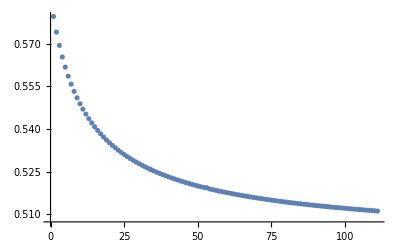

```mathematica
ListPlot[Table[1/n Log[NSum[(n^m/(m!))^(1/2),{m,n,∞}]],{n,10,120}]]
```

NumericalMath`NSequenceLimit::seqlim: The general form of the sequence could not be determined, and the result may be incorrect.

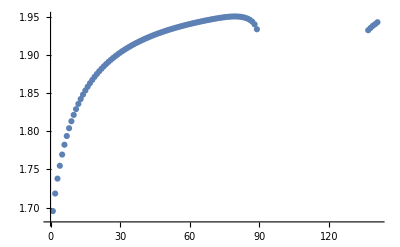

```mathematica
ListPlot[Table[1/n Log[NSum[(n^m/(m!))^2,{m,n,∞}]],{n,10,150}]]
```

```mathematica
Integrate[n^x/Gamma[x+1],{x,n,∞},Assumptions->n>0]
```

Integrate[n^x/Gamma[1+x],{x,n,∞},Assumptions→n>0]

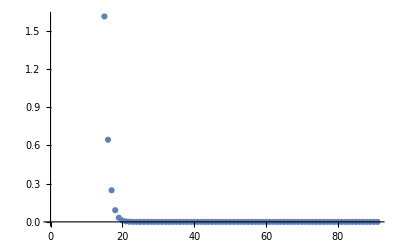

```mathematica
n=10;
ListPlot[Table[n^m/(m!),{m,n,100}]]
```

```mathematica
Stirling
```

```mathematica
Clear[n]
(n^m/(√(2π m)(m/ⅇ)^m))^α//FullSimplify
```

(ⅇ^m m^(-1/2-m) n^m)^α (2 π)^(-α/2)

```mathematica
Sum[(n^m/(m!))^α,{m,0,n}]
```

∑_(m=0)^n (n^m/(m!))^α

```mathematica
Integrate[n^x/Gamma[x+1],{x,0,n}]
```

∫_0^n n^x/Gamma[1+x]ⅆx

```mathematica
Integrate[n^x,{x,0,n}]
```

(-1+n^n)/Log[n]

```mathematica
∫_0^n 1/Gamma[1+x] ⅆx
```

∫_0^n 1/Gamma[1+x]ⅆx

```mathematica
Sum[(n^m/(m!))^α,{m,0,∞}]
```

∑_(m=0)^∞ (n^m/(m!))^α

```mathematica
Sum[n^(α m)/Gamma[α m +1],{m,0,∞}]
```

MittagLefflerE[α,n^α]

```mathematica
Integrate[Exp[n z](1-z)^n,{z,0,1}]
```

ConditionalExpression[ⅇ^n (-ExpIntegralE[-n,n]+n^-n Gamma[n]), Re[n]>-1]

```mathematica
Integrate[Exp[y]/(n!)(n-y)^n,{y,0,n}]
```

ConditionalExpression[(ⅇ^n (Gamma[1+n]-Gamma[1+n,n]))/(n!), Re[n]>-1]

```mathematica
Integrate[Exp[y]/(n!)(n-y)^n,{y,0,n/2}]
```

(ⅇ^n (Gamma[1+n,n/2]-Gamma[1+n,n]))/(n!)

```mathematica
Limit[(Gamma[1+n,n/2]-Gamma[1+n,n])/(n!),n->∞]
```

lim_(n→∞) (Gamma[1+n,n/2]-Gamma[1+n,n])/(n!)

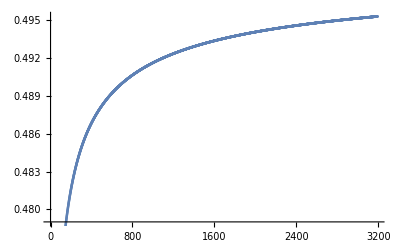

```mathematica
ListPlot[Table[(Gamma[1+n,n/2]-Gamma[1+n,n])/(n!),{n,10,3200}]]
```

```mathematica
D[Gamma[n+1],n]
```

Gamma[1+n] PolyGamma[0,1+n]

```mathematica
Limit[(n^n ⅇ^-n)/(Gamma[1+n] PolyGamma[0,1+n]),n->∞]
```

0

```mathematica
D[Gamma[n+1],{n,3}]
```

Gamma[1+n] PolyGamma[0,1+n]^3+3 Gamma[1+n] PolyGamma[0,1+n] PolyGamma[1,1+n]+Gamma[1+n] PolyGamma[2,1+n]

```mathematica
Integrate[t^n/(n!),{t,0,n/2}]
```

ConditionalExpression[(2^(-1-n) n^(1+n))/((1+n) n!), Re[n]>-1]

```mathematica
Limit[(2^(-1-n) n^(1+n))/((1+n) n!)ⅇ^(-n/3),n->∞]
```

0

```mathematica
Integrate[Exp[y]/(n!)(1-c)^n n^n,{y,0, c n}]
```

```mathematica
((1-c)^n (-1+ⅇ^(c n)) n^n)/(n!)//TeXForm
```

\frac{n^n (1-c)^n \left(e^{c n}-1\right)}{n!}

```mathematica
Limit[((1-c)^n (-1+ⅇ^(c n)) n^n)/(n!)Exp[- n]/.c->4/5,n->∞]
```

0

```mathematica
Limit[((1-c)^n (-1+ⅇ^(c n)) n^n)/(n!)Exp[- n],n->∞]
```

ConditionalExpression[0, c>0&&Log[1-c]<0&&c+Log[1-c]<0]

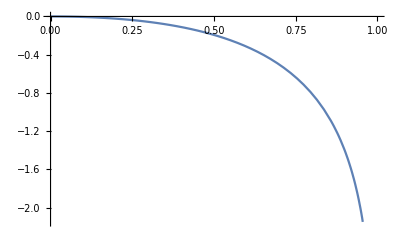

```mathematica
Plot[c + Log[1-c],{c,0,1}]
```

```mathematica
Limit[(n^n(1-c)^n(ⅇ^(c n)-1))/(ⅇ^n √(2 π n) (n/ⅇ)^n),n->∞]
```

ConditionalExpression[0, c>0&&Log[1-c]<0&&c+Log[1-c]<0]

```mathematica
(n^n(1-c)^n(ⅇ^(c n)-1))/(ⅇ^n √(2 π n) (n/ⅇ)^n)//FullSimplify
```

((1-c)^n (-1+ⅇ^(c n)))/(√n √(2 π))

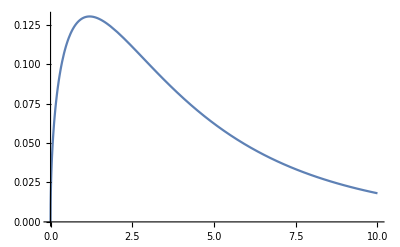

```mathematica
Plot[((1-c)^n (-1+ⅇ^(c n)))/(√n √(2 π))/.c->1/2,{n,0,10}]
```

```mathematica
Solve[Log[1-c] +c == 0, c]
```

Solve::ifun: Inverse functions are being used by Solve, so some solutions may not be found; use Reduce for complete solution information.

{{c→0}}

```mathematica
D[c+Log[1-c],c]//FullSimplify
```

c/(-1+c)

```mathematica
Limit[(n^n(1-c)^n(ⅇ^(c n)-1))/(ⅇ^(c n) √(2 π n) (n/ⅇ)^n),n->∞]
```

ConditionalExpression[0, c>0&&Log[1-c]<-1]

```mathematica
(n^n(1-c)^n(ⅇ^(c n)-1))/(ⅇ^(c n) √(2 π n) (n/ⅇ)^n)//FullSimplify
```

((1-c)^n ⅇ^(n-c n) (-1+ⅇ^(c n)))/(√n √(2 π))

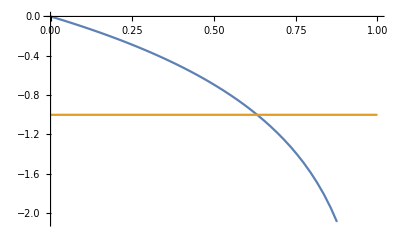

```mathematica
Plot[{Log[1-c],-1},{c,0,1}]
```

```mathematica
Solve[Log[1-c]==-1,c]//N
```

{{c→0.632121}}

```mathematica
Integrate[(n-y)^n/(n!),{y, c n , n},Assumptions->n>10]
```

(n-c n)^(1+n)/Gamma[2+n]

```mathematica
(n-c n)^(1+n)/Gamma[2+n] Exp[c n]//FullSimplify
```

(ⅇ^(c n) (n-c n)^(1+n))/Gamma[2+n]

```mathematica
Limit[(n-c n)^(1+n)/Gamma[2+n],n->∞,Assumptions->{0<c<1}]
```

ConditionalExpression[0, Log[1-c]<-1]

```mathematica
Limit[(n-c n)^(1+n)/Gamma[2+n],n->∞,Assumptions->{Log[1-c] > -1}]
```

ComplexInfinity

```mathematica
Solve[Log[1-c]==-1,c]
```

{{c→1-1/ⅇ}}

```mathematica
FullSimplify[(n-c n)^(1+n)/Gamma[2+n] √n/.c->1-1/ⅇ]
```

(ⅇ^(-1-n) n^(3/2+n))/Gamma[2+n]

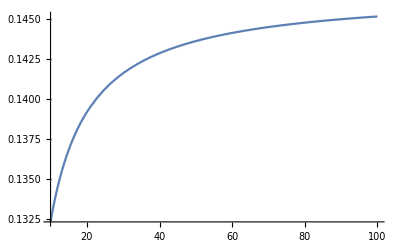

```mathematica
Plot[(ⅇ^(-1-n) n^(1+n))/Gamma[2+n] √n,{n,10,100}]
```

```mathematica
Limit[(ⅇ^(-1-n) n^(3/2+n))/Gamma[2+n],n->∞]
```

1/(ⅇ √(2 π))

```mathematica
Integrate[Exp[-y] y^n,{y,0,n},Assumptions->n>0]
```

Gamma[1+n]-Gamma[1+n,n]

```mathematica
n^n/(√(2π n) (n/ⅇ)^n)//FullSimplify
```

ⅇ^n/(√n √(2 π))

```mathematica
n^(n-1)/(√(2π (n-1)) ((n-1)/ⅇ)^(n-1))//FullSimplify
```

```mathematica
(ⅇ^(-1+n) (-1+n)^(1/2-n) n^(-1+n))/(√(2 π))//TeXForm
```

\frac{e^{n-1} (n-1)^{\frac{1}{2}-n} n^{n-1}}{\sqrt{2 \pi }}

```mathematica
Integrate[Exp[-z] z^{n-1},{z,0,∞}]
```

{ConditionalExpression[Gamma[n], Re[n]>0]}

```mathematica
Limit[n^(n-1)/((n-1)!)Exp[-n],n->∞]
```

0

```mathematica
Limit[(-1+n)^-n n^(+n),n->∞]
```

ⅇ

```mathematica
(ⅇ^n (-1+n)^(1/2) n^-1)/(√(2 π))//FullSimplify
```

(ⅇ^n √(-1+n))/(n √(2 π))

```mathematica
-ⅇ^n/(√(2 π n)) + ⅇ^n - ⅇ^n/(√(2 π n))(√((π n)/2)-1/3+(√(2π))/(24 √n) - 4/(135 n))//FullSimplify//Expand
```

ⅇ^n/2-ⅇ^n/(24 n)+(2 ⅇ^n √(2/π))/(135 n^(3/2))-(ⅇ^n √(2/π))/(3 √n)

```mathematica
j
```

```mathematica
Series[(45 √n (-1+12 n)+8 (2-45 n) √(2/π))/(1080 n^(3/2))]
```